```mathematica
HamiltonianLTFI[g_, h_]:={{2h+2, -g, -g, 0}, {-g, -2, 0, -g}, {-g, 0, -2, -g}, {0, -g, -g, -2h+2}};
```

```mathematica
MatrixForm[HamiltonianLTFI[g, h]]
```

(2+2 h | -g | -g | 0
-g | -2 | 0 | -g
-g | 0 | -2 | -g
0 | -g | -g | 2-2 h)

```mathematica
Assuming[h>0 && g >0,Eigensystem[HamiltonianLTFI[g, h]]]
```

{{-2,Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1],Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2],Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]},{{0,-1,1,0},{-1+1/(2 g^2)(2+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1]) (-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1]),-(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1])/(2 g),-(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1])/(2 g),1},{-1+1/(2 g^2)(2+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2]) (-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2]),-(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2])/(2 g),-(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2])/(2 g),1},{-1+1/(2 g^2)(2+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]) (-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]),-(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3])/(2 g),-(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3])/(2 g),1}}}

```mathematica
Grid[%4]
```

-2 | Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1] | Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2] | Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]
{0,-1,1,0} | {-1+1/(2 g^2)(2+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1]) (-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1]),-1/(2 g)(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1]),-1/(2 g)(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,1]),1} | {-1+1/(2 g^2)(2+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2]) (-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2]),-1/(2 g)(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2]),-1/(2 g)(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,2]),1} | {-1+1/(2 g^2)(2+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]) (-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]),-1/(2 g)(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]),-1/(2 g)(-2+2 h+Root[8+8 g^2-8 h^2+(-4-4 g^2-4 h^2) #1-2 #1^2+#1^3&,3]),1}

```mathematica
(*Along g=0 axis*)
Assuming[h>0 ,Eigensystem[HamiltonianLTFI[0, h]]]
```

{{-2,-2,2 (1-h),2 (1+h)},{{0,0,1,0},{0,1,0,0},{0,0,0,1},{1,0,0,0}}}

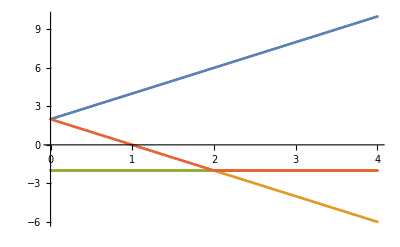

```mathematica
ListPlot[{Table[{h, N[Eigenvalues[HamiltonianLTFI[0, h]][[1]]]}, {h, 0, 4, 0.01}],Table[{h, N[Eigenvalues[HamiltonianLTFI[0, h]][[2]]]}, {h, 0, 4, 0.01}],Table[{h, N[Eigenvalues[HamiltonianLTFI[0, h]][[3]]]}, {h, 0, 4, 0.01}],Table[{h, N[Eigenvalues[HamiltonianLTFI[0, h]][[4]]]}, {h, 0, 4, 0.01}]}]
```

```mathematica
(*Along h=1 axis*)
Assuming[g>0 ,Eigensystem[HamiltonianLTFI[g, 1]]]
```

{{-2,Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,1],Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,2],Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,3]},{{0,-1,1,0},{-1+(Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,1] (2+Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,1]))/(2 g^2),-Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,1]/(2 g),-Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,1]/(2 g),1},{-1+(Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,2] (2+Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,2]))/(2 g^2),-Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,2]/(2 g),-Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,2]/(2 g),1},{-1+(Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,3] (2+Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,3]))/(2 g^2),-Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,3]/(2 g),-Root[8 g^2+(-8-4 g^2) #1-2 #1^2+#1^3&,3]/(2 g),1}}}

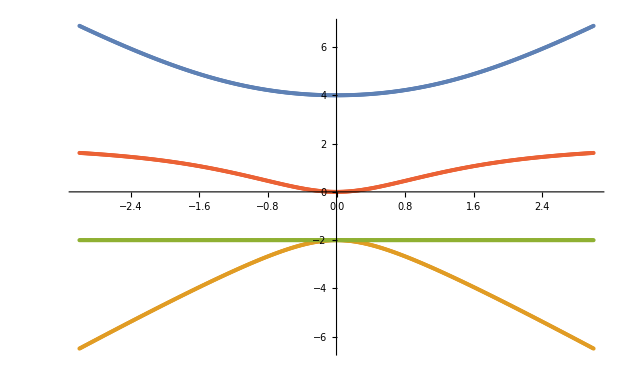

```mathematica
ListPlot[{Table[{g, N[Eigenvalues[HamiltonianLTFI[g, 1]][[1]]]}, {g, -3, 3, 0.01}],Table[{g, N[Eigenvalues[HamiltonianLTFI[g, 1]][[2]]]}, {g, -3, 3, 0.01}],Table[{g, N[Eigenvalues[HamiltonianLTFI[g, 1]][[3]]]}, {g, -3, 3, 0.01}],Table[{g, N[Eigenvalues[HamiltonianLTFI[g, 1]][[4]]]}, {g, -3, 3, 0.01}]}]
```